## Filtering function for different spin echo regime

```mathematica
integral[ω_,ϕ_,t_]:=integral[ω,ϕ,t]=(-Cos[ω*t+ϕ])/ω;
τe=1/30;    (* Total free evolution time*)
τc= 6.0*10^-3; (* Collisional gate time (field-sensitive time) *)
t0= 0*10^-3; (* delay between pi/2 pulse and transferring to collisional states *)
residue[ω_,ϕ_,t_]:=integral[ω,ϕ,t+τc]-integral[ω,ϕ,t]-integral[ω,ϕ,t+τc+τe/2]+integral[ω,ϕ,t+τe/2];
residue2[ω_,ϕ_,t_]:=integral[ω,ϕ,t+τc]-integral[ω,ϕ,t];
```

```mathematica
filterList6 = Table[
Mean[Table[residue[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.1}
];
freq=Table[f,{f,0.1,1000,0.1}];
```

```mathematica
filterList16no = Table[
Mean[Table[residue2[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.05}
];
```

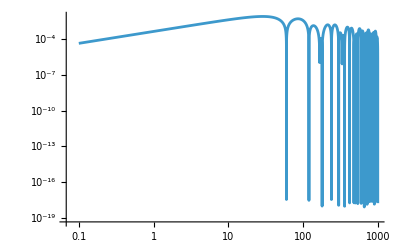

Transpose::nmtx: The first two levels of {{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,«9950»},{0.0117087,«49»,«19949»}} cannot be transposed.

ListLogLogPlot::lpn: {{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,«19»,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,«9950»},{«1»}}^T is not a list of numbers or pairs of numbers.

```mathematica
plotlist6=Transpose[{freq,Sqrt[filterList6]}];
p1=ListLogLogPlot[plotlist6,PlotRange->All,Joined->True]
plotlist16no=Transpose[{freq,Sqrt[filterList16no]}];
p1no=ListLogLogPlot[plotlist16no,PlotRange->All,Joined->True]
```

```mathematica
delayList = Table [Total[Table[
Mean[Table[residue[2Pi*f,ϕ,t]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,3000,1}]],{t,0,6*10^-3,1*10^-3}
]
(* 
Verify that delay doesn't matter 
{0.004983085677225189,0.004983106650688737,0.0049831066721469685,0.004983106675922084,0.004983106677133457,0.00498310667763244,0.004983106677865132}
*)
```

{0.0083078,0.00830782,0.00830782,0.00830782,0.00830782,0.00830782,0.00830782}

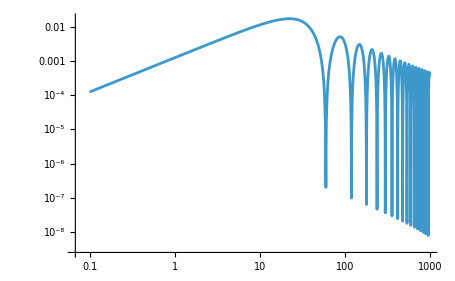

```mathematica
filterList8 = Table[
Mean[Table[residue[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.5}
];
freq=Table[f,{f,0.1,1000,0.5}];
plotlist8=Transpose[{freq,Sqrt[filterList8]}];
p2=ListLogLogPlot[plotlist8,PlotRange->All,Joined->True]
```

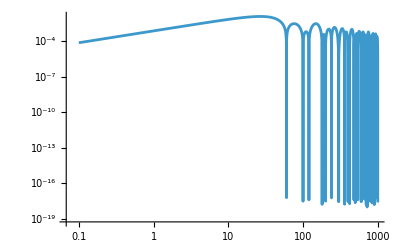

```mathematica
filterList10 = Table[
Mean[Table[residue[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.1}
];
freq=Table[f,{f,0.1,1000,0.1}];
plotlist10=Transpose[{freq,Sqrt[filterList10]}];
p3=ListLogLogPlot[plotlist10,PlotRange->All,Joined->True]
```

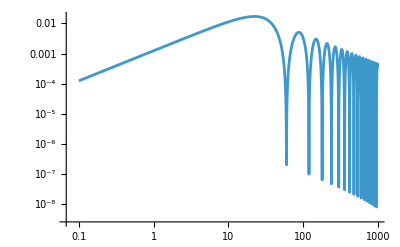

```mathematica
filterList12 = Table[
Mean[Table[residue[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.5}
];
freq=Table[f,{f,0.1,1000,0.5}];
plotlist12=Transpose[{freq,Sqrt[filterList12]}];
p4=ListLogLogPlot[plotlist12,PlotRange->All,Joined->True]
```

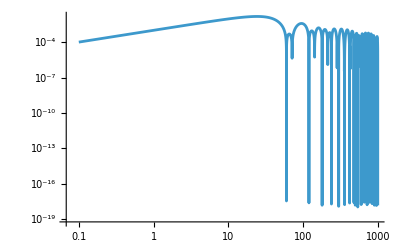

```mathematica
filterList14 = Table[
Mean[Table[residue[2Pi*f,ϕ,0]^2,{ϕ,0,2Pi,2*Pi/200}]],
{f,0.1,1000,0.1}
];
freq=Table[f,{f,0.1,1000,0.1}];
plotlist14=Transpose[{freq,Sqrt[filterList14]}];
p5=ListLogLogPlot[plotlist14,PlotRange->All,Joined->True]
```

```mathematica
p1=ListLogLogPlot[plotlist6,PlotRange->{{0.1,10^3},{10^-7,0.25*10^-1}},Joined->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-10,4}],None},{Table[{10^k,Superscript[10,k]},{k,-5,4}],None}},
GridLines->Automatic,
Frame->True,Axes->False,
FrameTicksStyle->Directive[18],ImageSize->Large,
FrameStyle->Thick,ImageSize->Large,
PlotStyle->ColorData[97,"ColorList"][[1]]];
(*p2=ListLogLogPlot[plotlist8,PlotRange->All,Joined->True,PlotStyle->ColorData[97,"ColorList"][[3]]];*)
p3=ListLogLogPlot[plotlist10,PlotRange->All,Joined->True,PlotStyle->ColorData[97,"ColorList"][[2]]];
(*p4=ListLogLogPlot[plotlist12,PlotRange->All,Joined->True,PlotStyle->ColorData[97,"ColorList"][[2]]];*)
p5=ListLogLogPlot[plotlist14,PlotRange->All,Joined->True,PlotStyle->ColorData[97,"ColorList"][[3]]];
```

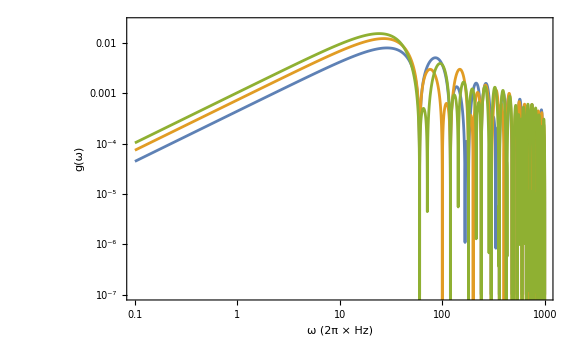

```mathematica
Show[p1,p3,p5,
Frame->True,
FrameStyle->Thick,
FrameLabel->{Style["ω (2π × Hz)",FontSize->22],
Style["g(ω)",FontSize->22,FontFamily->"Helvetica"]},
Epilog->Inset[Framed[Column[{
LineLegend[{ColorData[97,"ColorList"][[1]]},{"6 ms"},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->16]],
LineLegend[{ColorData[97,"ColorList"][[2]]},{"10 ms"},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->16]],
LineLegend[{ColorData[97,"ColorList"][[3]]},{"14 ms"},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->16]]
}],
RoundingRadius->5],Scaled[{0.11,0.18}]]
]
```

```mathematica
Sqrt[Total[filterList16]]
```

0.128503

```mathematica
Sqrt[Total[filterList14]]
```

0.117885

```mathematica
Sqrt[Total[filterList12]]
```

0.109077

```mathematica
Sqrt[Total[filterList10]]
```

0.0994895

```mathematica
Sqrt[Total[filterList8]]
```

0.0888729

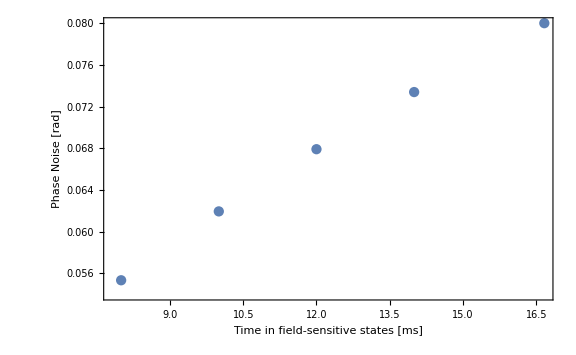

```mathematica
noiseList = {Sqrt[Total[filterList8]],Sqrt[Total[filterList10]],Sqrt[Total[filterList12]],Sqrt[Total[filterList14]],Sqrt[Total[filterList16]]}/Sqrt[Total[filterList16]]*0.08;
timelist = {8,10,12,14,16.666};
noiseplot = Transpose[{timelist,noiseList}];
p01 = ListPlot[noiseplot,ImageSize->Large,Frame->True,FrameStyle->Thick,
FrameTicksStyle->Directive[16,Italic],
FrameLabel->{Style["Time in field-sensitive states [ms]",FontSize->20],Style["Phase Noise [rad]",FontSize->20,FontFamily->"Helvetica"]}]
```

```mathematica
Epilog->Inset[Framed[Column[{LineLegend[{RGBColor[0.368417, 0.506779, 0.709798]},{"16.666 ms "},LabelStyle->Medium],
LineLegend[{ColorData[97,"ColorList"][[2]]},{"12 ms"},LabelStyle->Medium],LineLegend[{ColorData[97,"ColorList"][[3]]},{"8 ms"},LabelStyle->Medium]}],
RoundingRadius->5],Scaled[{0.25,0.35}]]
```

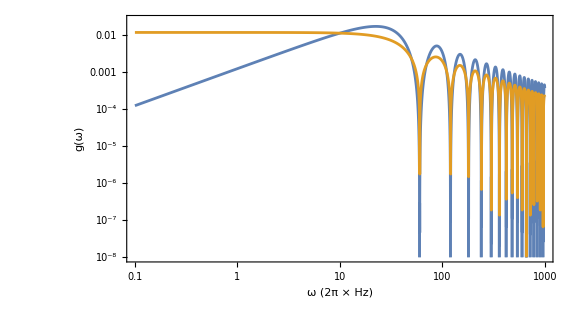

```mathematica
p1s=ListLogLogPlot[plotlist16,PlotRange->{{0.1,1*10^3},{10^-8,0.25*10^-1}},Joined->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-10,4}],None},{Table[{10^k,Superscript[10,k]},{k,-5,4}],None}},
GridLines->Automatic,
Frame->True,Axes->False,
FrameTicksStyle->Directive[18],ImageSize->Large,
FrameStyle->Thick,ImageSize->Large,
PlotStyle->ColorData[97,"ColorList"][[1]]];
p1sno=ListLogLogPlot[plotlist16no,PlotRange->All,Joined->True,PlotStyle->ColorData[97,"ColorList"][[2]]];
Show[p1s,p1sno,
Frame->True,
FrameStyle->Thick,
AspectRatio->7/13,
FrameLabel->{Style["ω (2π × Hz)",FontSize->22],
Style["g(ω)",FontSize->22,FontFamily->"Helvetica"]},
Epilog->Inset[Framed[Column[{
LineLegend[{ColorData[97,"ColorList"][[1]]},{"Spin Echo"},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->16]],
LineLegend[{ColorData[97,"ColorList"][[2]]},{"Single Leg"},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->16]]
}],
RoundingRadius->5],Scaled[{0.15,0.15}]]
]
```